Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

5 - 18 Harmonic functions in a disk
Using (7), find the potential Φ[r,θ] in the unit disk r<1 having the given boundary values Φ[1,θ]. Using the sum of the first few terms of the series, compute some values of Φ and sketch a figure of the equipotential lines.

Before I get started, I want to show a plot of the function of example 1, p. 780. The plot looks quite a bit like figure 424, except that the contour lines do not tally exactly with the contour line values in figure 424. It is surprising that as far as the accuracy of contour lines is concerned (as determined by cursor hovering over the contour line) 16 terms of the Fourier series yields the same accuracy as 256 terms.

```mathematica
sampl=1/2+4/π^2 Sum[r^(2n-1)Cos[(2 n-1) θ]/(2 n-1)^2,{n,1,16}];
```

```mathematica
p1=ContourPlot[ sampl,{r,θ}∈Disk[{0,0},1],ImageSize->200,Contours->9,Axes->True,AxesLabel->{x,y},Epilog->{{Red,Line[{{0,0},{1,Sin[π/8]}}]},{Blue,Point[{0.0,0.0 0.38262}]},{Blue,Point[{0.1,0.1 0.38262}]},{Blue,Point[{0.2,0.2 0.38262}]},{Blue,Point[{0.3,0.3 0.38262}]},{Blue,Point[{0.4,0.4 0.38262}]},{Blue,Point[{0.5,0.5 0.38262}]},{Blue,Point[{0.6,0.6 0.38262}]},{Blue,Point[{0.7,0.7 0.38262}]},{Blue,Point[{0.8,0.8 0.38262}]},{Blue,Point[{0.8,0.8 0.38262}]},{Blue,Point[{0.9,0.9 0.38262}]}}];
```

The table of points below may hold some insight into the plot information, because evaluated point values can be compared with their plotted contour swath.

```mathematica
Table[{r,r Sin[θ],N[Evaluate[sampl]]},{r,0,0.9,0.1}]/.θ->π/8
```

{{0.,0.,0.5},{0.1,0.0382683,0.537461},{0.2,0.0765367,0.575023},{0.3,0.114805,0.612779},{0.4,0.153073,0.650799},{0.5,0.191342,0.689108},{0.6,0.22961,0.727638},{0.7,0.267878,0.766151},{0.8,0.306147,0.80414},{0.9,0.344415,0.840759}}

Note that since the largest r value on x axis would be 0.92388, the plotting stops at 0.9.

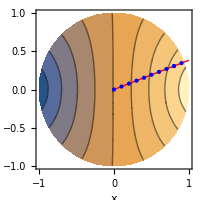

```mathematica
Row[{p1}]
```

```mathematica
N[Sin[π/8]]
```

0.382683

```mathematica
N[Cos[π/8]]
```

0.92388

5.  Φ[1,θ]=3/2 Sin[3 θ]

```mathematica
Clear["Global`*"]
```

The method I use to get to the answer is the same as in problem 7, which I worked first, and which has more explanatory comments. The method is simply to compare the given boundary condition with numbered line (7), p 780, and recognize that things already look pretty good as they are. Mainly I have a sine function, which is the core of the integral. I have a nice definite, real fraction which I can consider to be a_0. I don’t need a cosine factor. The only thing I need, if my reasoning is correct, or at least consistent, is an r factor. The exponent of the r factor I want will be equal to the coefficient on the sine, so I need an r^3. Thus

```mathematica
Φ[1,θ]=(3 r^3)/2 Sin[3 θ]
```

The answer above agrees with the answer in the text. Next a table of values, which correlate with the points in the plot below.

```mathematica
Table[{r,r Sin[θ],N[Evaluate[(3 r^3)/2 Sin[3 θ]]]},{r,0,0.9,0.1}]/.θ->π/8
```

{{0.,0.,0.},{0.1,0.0382683,0.00138582},{0.2,0.0765367,0.0110866},{0.3,0.114805,0.0374171},{0.4,0.153073,0.0886924},{0.5,0.191342,0.173227},{0.6,0.22961,0.299337},{0.7,0.267878,0.475336},{0.8,0.306147,0.709539},{0.9,0.344415,1.01026}}

In the plot below, the quadrants are separated by squarish contour lines having value of zero. It seems a little odd that although the plotted function is exact, contour boundaries, especially along the y-axis, look ragged. And what about the r=0.7,r=0.8, and r=0.9 points on the plot? They look dispossessed.

```mathematica
p1=ContourPlot[ (3 r^3)/2 Sin[3 θ],{r,θ}∈Disk[{0,0},1],ImageSize->200,Contours->9,Axes->True,AxesLabel->{x,y},Epilog->{{Red,Line[{{0,0},{1,Sin[π/8]}}]},{Blue,Point[{0.0,0.0 0.38262}]},{Blue,Point[{0.1,0.1 0.38262}]},{Blue,Point[{0.2,0.2 0.38262}]},{Blue,Point[{0.3,0.3 0.38262}]},{Blue,Point[{0.4,0.4 0.38262}]},{Blue,Point[{0.5,0.5 0.38262}]},{Blue,Point[{0.6,0.6 0.38262}]},{Blue,Point[{0.7,0.7 0.38262}]},{Blue,Point[{0.8,0.8 0.38262}]},{Green,Point[{0.8,0.8 0.38262}]},{Brown,Point[{0.9,0.9 0.38262}]}}];
```

```mathematica
p2=ContourPlot[ (3 r^3)/2 Sin[3/8 θ],{r,θ}∈Disk[{0,0},1],ImageSize->200,Contours->9,Axes->True,AxesLabel->{x,y},PlotRange->{{0,1.1},{0,0.4}},AspectRatio->Automatic,Epilog->{{Red,Line[{{0,0},{1,Sin[π/8]}}]},{Blue,Point[{0.0,0.0 0.38262}]},{Blue,Point[{0.1,0.1 0.38262}]},{Blue,Point[{0.2,0.2 0.38262}]},{Blue,Point[{0.3,0.3 0.38262}]},{Blue,Point[{0.4,0.4 0.38262}]},{Blue,Point[{0.5,0.5 0.38262}]},{Blue,Point[{0.6,0.6 0.38262}]},{Blue,Point[{0.7,0.7 0.38262}]},{Blue,Point[{0.8,0.8 0.38262}]},{Green,Point[{0.8,0.8 0.38262}]},{Brown,Point[{0.9,0.9 0.38262}]}}];
```

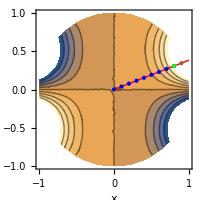
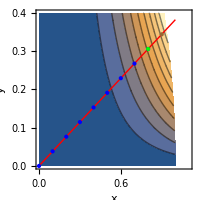

```mathematica
Row[{p1,p2}]
```

The left plot is framed in terms of the problem function, so it claims place.  It shows test points, but it’s not fair to plot test points on a function that has been altered for testing. Thus the right plot, which shows the form the function will assume at the time the line of test points is placed on it.

7.  Φ[1,θ]=a Cos[4 θ]^2

```mathematica
Clear["Global`*"]
```

The solution to this problem is very easy if I make one particular assumption, which is that the a posited in the boundary condition of the problem is not just some a made up arbitrarily, but is in fact the same a which is contained in numbered line (7) on p. 780.

My line of reasoning also depends on an identity stated in numbered line (10) on text p. A-64 (in Appendix 3), which goes like so
cos^2 x = 1/2 + 1/2 cos 2x  or, cos^2 x = 1/2 + 1/2 cos 2x.

Extending the identity to the boundary condition means that Cos[4 θ]^2 = 1/2 + 1/2Cos[8 θ]. So now I build the chain

```mathematica
Φ[1,θ]=a Cos[4 θ]^2=a(1/2+1/2 Cos[8 θ])=a/2+a/2 Cos[8 θ]
```

Looking at the final expression on the right and comparing with numbered line (7) on p. 780 could mean I am nearly finished if I take a certain line of reasoning, like the following. The unsubscripted a is such as to take precedence over any subscripted ones, and therefore I don’t need to worry about finding any subscripted a by use of numbered line (8). If the cosine factor is already there, I don’t need to worry about a possible sine factor, it must be null, because that is the pattern of Fourier-related integrals which contain both a_n and b_n. The only thing left to think about is the r/R factor. Since I am on the unit circle, I’ll take R=1. The exponent of the r/R factor is synchronized with the coefficient of the angle θ, and since there it is 8, I must need an r^8. So I just toss in r^8, giving

```mathematica
a/2+(a r^8)/2 Cos[8 θ]
```

Voilà, ze answer agrees with ze text. Next comes the table of test values.

```mathematica
Table[{r,r Sin[θ],N[Evaluate[a/2+(a r^8)/2 Cos[8 θ]]]},{r,0,0.9,0.1}]/.{θ->π/8,a->1}
```

{{0.,0.,0.5},{0.1,0.0382683,0.5},{0.2,0.0765367,0.499999},{0.3,0.114805,0.499967},{0.4,0.153073,0.499672},{0.5,0.191342,0.498047},{0.6,0.22961,0.491602},{0.7,0.267878,0.471176},{0.8,0.306147,0.416114},{0.9,0.344415,0.284766}}

For the plot, I can’t get anything to show for any value of a I tried to insert with postfix substitution. However, if I enter an a value directly, Mathematica will show me something. After trying several values of a, I found no great variety of plots, so as far as a goes, so I’ll just stick to the one.

```mathematica
p1=ContourPlot[ 1/2+(1 r^8)/2 Cos[8 θ],{r,θ}∈Disk[{0,0},1],ImageSize->200,Contours->9,Axes->True,AxesLabel->{x,y},Epilog->{{Red,Line[{{0,0},{1,Sin[π/8]}}]},{Blue,Point[{0.0,0.0 0.38262}]},{Blue,Point[{0.1,0.1 0.38262}]},{Blue,Point[{0.2,0.2 0.38262}]},{Blue,Point[{0.3,0.3 0.38262}]},{Blue,Point[{0.4,0.4 0.38262}]},{Blue,Point[{0.5,0.5 0.38262}]},{Blue,Point[{0.6,0.6 0.38262}]},{Blue,Point[{0.7,0.7 0.38262}]},{Blue,Point[{0.8,0.8 0.38262}]},{Green,Point[{0.8,0.8 0.38262}]},{Brown,Point[{0.9,0.9 0.38262}]}}];
```

Now to show a plot of the function with the points in the table for comparison.

```mathematica
p2=ContourPlot[ 1/2+(1 r^8)/2 Cos[π],{r,θ}∈Disk[{0,0},1],ImageSize->200,Contours->9,Axes->True,AxesLabel->{x,y},PlotRange->{{0,1.1},{0,0.4}},AspectRatio->Automatic,Epilog->{{Red,Line[{{0,0},{1,Sin[π/8]}}]},{Blue,Point[{0.0,0.0 0.38262}]},{Blue,Point[{0.1,0.1 0.38262}]},{Blue,Point[{0.2,0.2 0.38262}]},{Blue,Point[{0.3,0.3 0.38262}]},{Blue,Point[{0.4,0.4 0.38262}]},{Blue,Point[{0.5,0.5 0.38262}]},{Blue,Point[{0.6,0.6 0.38262}]},{Blue,Point[{0.7,0.7 0.38262}]},{Blue,Point[{0.8,0.8 0.38262}]},{Green,Point[{0.8,0.8 0.38262}]},{Brown,Point[{0.9,0.9 0.38262}]}}];
```

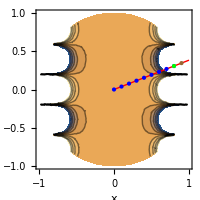
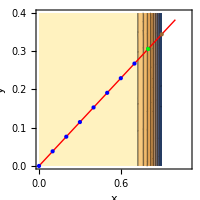

```mathematica
Row[{p1,p2}]
```

Again, here, at left, is a plot of a sort of generalized function, and superimposed on it is a line of test points which do not fully relate to it. At right the function is allowed to modify itself to accommodate the conditions of the test.

9.  Φ[1,θ]=8 Sin[θ]^4

```mathematica
Clear["Global`*"]
```

First I try calling for a Fourier series. I notice that no matter how many terms I call for, it only gives me five.

```mathematica
FourierSeries[8 Sin[θ]^4,θ,16]
```

3-2 ⅇ^(-2 ⅈ θ)-2 ⅇ^(2 ⅈ θ)+1/2 ⅇ^(-4 ⅈ θ)+1/2 ⅇ^(4 ⅈ θ)

I think I need to put it in the terms which the text likes to work with.

```mathematica
ExpToTrig[%]
```

3-4 Cos[2 θ]+Cos[4 θ]

Sure enough, this worked like a charm once again. The only thing missing at this point is the r^n factor. The constant term, not having a cosine term whose coefficient it could re-purpose as exponent, gives me some misgivings, so I won’t attach an r to that one.

```mathematica
3-4 r^2 Cos[2 θ]+r^4 Cos[4 θ]
```

I see that there is not an ellipsis in the text answer, so I have to believe that this is all there is of it.

Making a table of values.

```mathematica
Table[{r,r Sin[θ],N[Evaluate[3-4 r^2 Cos[2 θ]+r^3 Cos[4 θ]]]},{r,0,0.9,0.1}]/.{θ->π/8}
```

{{0.,0.,3.},{0.1,0.0382683,2.97172},{0.2,0.0765367,2.88686},{0.3,0.114805,2.74544},{0.4,0.153073,2.54745},{0.5,0.191342,2.29289},{0.6,0.22961,1.98177},{0.7,0.267878,1.61407},{0.8,0.306147,1.18981},{0.9,0.344415,0.708974}}

```mathematica
ContourPlot[ 3-4 r^2 Cos[2 θ]+r^3 Cos[4 θ],{r,θ}∈Disk[{0,0},1],ImageSize->200,Contours->9,Axes->True,AxesLabel->{x,y},Epilog->{{Red,Line[{{0,0},{1,Sin[π/8]}}]},{Blue,Point[{0.0,0.0 0.38262}]},{Blue,Point[{0.1,0.1 0.38262}]},{Blue,Point[{0.2,0.2 0.38262}]},{Blue,Point[{0.3,0.3 0.38262}]},{Blue,Point[{0.4,0.4 0.38262}]},{Blue,Point[{0.5,0.5 0.38262}]},{Blue,Point[{0.6,0.6 0.38262}]},{Blue,Point[{0.7,0.7 0.38262}]},{Blue,Point[{0.8,0.8 0.38262}]},{Green,Point[{0.8,0.8 0.38262}]},{Brown,Point[{0.9,0.9 0.38262}]}}]
```

All the table points are present on the table and the function values even look reasonable.

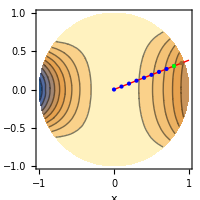

11.  Φ[1,θ]=θ/π  if -π<θ<π

```mathematica
Clear["Global`*"]
```

First to define the piecewise function. If I define one little piece, it seems like I have to make some statement about the intervals outside of that. So I’ll try

```mathematica
Φ[1,θ_]=Piecewise[{{θ/π, -π<θ<π}, {0, θ<-π∨π<θ}}]
```

Piecewise[{{θ/π, -π<θ<π}, {0, True}}]

I did problem 13 before I did this one. Like I did there, I will call for a Fourier’s series and see what happens.

```mathematica
FourierSeries[Φ[1,θ],θ,8];
```

Unlike problem 9, there is no finite termination which I run into with this series.

```mathematica
ExpToTrig[%]
```

(2 Sin[θ])/π-Sin[2 θ]/π+(2 Sin[3 θ])/(3 π)-Sin[4 θ]/(2 π)+(2 Sin[5 θ])/(5 π)-Sin[6 θ]/(3 π)+(2 Sin[7 θ])/(7 π)-Sin[8 θ]/(4 π)

I want to try to put the answer into a form of sum with general terms

```mathematica
Simplify[FindSequenceFunction[{2,-1,2/3,-1/2,2/5,-1/3,2/7,-1/4,2/9},n]]
```

-(2 (-1)^n)/n

So I think it should look like

```mathematica
prob11=Sum[-(2 (-1)^n)/n r^n Sin[n θ]/π,{n,1,8}]
```

(2 r Sin[θ])/π-(r^2 Sin[2 θ])/π+(2 r^3 Sin[3 θ])/(3 π)-(r^4 Sin[4 θ])/(2 π)+(2 r^5 Sin[5 θ])/(5 π)-(r^6 Sin[6 θ])/(3 π)+(2 r^7 Sin[7 θ])/(7 π)-(r^8 Sin[8 θ])/(4 π)

The answer in the above cell matches that of the text. (The text answer elects to factor out 2/π as a leading factor.)

The problem asked for some sample values and a plot. But the 5th contour line lays on top of the y-axis pretty well, making me feel the limited terms used represent the series pretty well.

```mathematica
Table[{r,r Sin[θ],N[Evaluate[prob11]]},{r,0,0.9,0.1}]/.θ->π/8
```

{{0.,0.,0.},{0.1,0.0382683,0.0222928},{0.2,0.0765367,0.0410687},{0.3,0.114805,0.0570731},{0.4,0.153073,0.0708642},{0.5,0.191342,0.0828772},{0.6,0.22961,0.0934878},{0.7,0.267878,0.103091},{0.8,0.306147,0.112215},{0.9,0.344415,0.121684}}

```mathematica
p1=ContourPlot[ prob11,{r,θ}∈Disk[{0,0},1],ImageSize->200,Contours->9,Axes->True,AxesLabel->{x,y},Epilog->{{Red,Line[{{0,0},{1,Sin[π/8]}}]},{Blue,Point[{0.0,0.0 0.38262}]},{Blue,Point[{0.1,0.1 0.38262}]},{Blue,Point[{0.2,0.2 0.38262}]},{Blue,Point[{0.3,0.3 0.38262}]},{Blue,Point[{0.4,0.4 0.38262}]},{Blue,Point[{0.5,0.5 0.38262}]},{Blue,Point[{0.6,0.6 0.38262}]},{Blue,Point[{0.7,0.7 0.38262}]},{Blue,Point[{0.8,0.8 0.38262}]},{Green,Point[{0.8,0.8 0.38262}]},{Brown,Point[{0.9,0.9 0.38262}]}}];
```

```mathematica
p2=ContourPlot[ prob11,{r,θ}∈Disk[{0,0},1],ImageSize->200,Contours->9,Axes->True,AxesLabel->{x,y},PlotRange->{{0,1.1},{0,0.4}},AspectRatio->Automatic,Epilog->{{Red,Line[{{0,0},{1,Sin[π/8]}}]},{Blue,Point[{0.0,0.0 0.38262}]},{Blue,Point[{0.1,0.1 0.38262}]},{Blue,Point[{0.2,0.2 0.38262}]},{Blue,Point[{0.3,0.3 0.38262}]},{Blue,Point[{0.4,0.4 0.38262}]},{Blue,Point[{0.5,0.5 0.38262}]},{Blue,Point[{0.6,0.6 0.38262}]},{Blue,Point[{0.7,0.7 0.38262}]},{Blue,Point[{0.8,0.8 0.38262}]},{Green,Point[{0.8,0.8 0.38262}]},{Brown,Point[{0.9,0.9 0.38262}]}}];
```

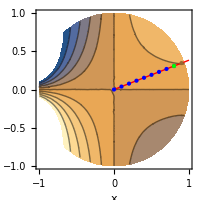
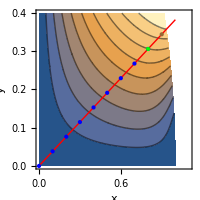

```mathematica
Row[{p1,p2}]
```

In this plot I lucked out because the quadrant I have test points for is not distorted. Still the function values for r=0.7, r=0.8, and r=0.9 do not seem plausible on the left plot. As I did with problem 7, I show an altered plot with altered function for a specified test value of θ on the right. The test points do land on the plot, but the last few do not seem as large as expected. There must be something wrong, or else the discrepancy may be due to the ContourPlot evaluation process discussed by george2079 in StackExchangeMma question 75352.

13. Φ[1,θ]=θ  if -1/2 π<θ<1/2 π and 0 otherwise

```mathematica
Clear["Global`*"]
```

First I define the piecewise function. I see that Mathematica can work well with a piecewise function even if I don’t specifically call it that.

```mathematica
Φ[1,θ_]=Piecewise[{{θ, -1/2 π<θ<1/2 π}, {0, θ<-1/2 π∨1/2 π<θ}}]
```

Piecewise[{{θ, -π/2<θ<π/2}, {0, True}}]

Knowing that Poisson’s integral formula is closely related to Fourier series,  I’ll call for another one.

```mathematica
FourierSeries[Φ[1,θ],θ,12];
```

```mathematica
ExpToTrig[%]
```

(2 Sin[θ])/π+1/2 Sin[2 θ]-(2 Sin[3 θ])/(9 π)-1/4 Sin[4 θ]+(2 Sin[5 θ])/(25 π)+1/6 Sin[6 θ]-(2 Sin[7 θ])/(49 π)-1/8 Sin[8 θ]+(2 Sin[9 θ])/(81 π)+1/10 Sin[10 θ]-(2 Sin[11 θ])/(121 π)-1/12 Sin[12 θ]

The above cell is looking pretty good. In fact it looks like it’s there except for the r^n factor. But instead of just sticking it in, (as is done in example 1 p. 780), I can’t resist trying to build a general expression. It turns out that FindSequenceFunction can’t handle the whole complicated sequence at once, so I’ll have to try to write it for staggered, or “hop-along” incrementation,

```mathematica
Simplify[FindSequenceFunction[{1,9,25,49,81,121},n]]
```

(1-2 n)^2

```mathematica
Simplify[FindSequenceFunction[{2,-4,6,-8,10,-12},n]]
```

-2 (-1)^n n

```mathematica
prob13=Sum[(2 Sin[(2n-1)θ] r^(2 n-1))/((-1)^(n-1)(1-2 n)^2 π)+(1 r^(2 n))/(-2 (-1)^n n)Sin[2n θ],{n,1,4}]
```

(2 r Sin[θ])/π+1/2 r^2 Sin[2 θ]-(2 r^3 Sin[3 θ])/(9 π)-1/4 r^4 Sin[4 θ]+(2 r^5 Sin[5 θ])/(25 π)+1/6 r^6 Sin[6 θ]-(2 r^7 Sin[7 θ])/(49 π)-1/8 r^8 Sin[8 θ]

The above cell matches the answer in the text.

Again a table and a plot.

```mathematica
Table[{r,r Sin[θ],N[Evaluate[prob13]]},{r,0,0.9,0.1}]/.θ->π/8
```

{{0.,0.,0.},{0.1,0.0382683,0.0278079},{0.2,0.0765367,0.0619591},{0.3,0.114805,0.101259},{0.4,0.153073,0.144151},{0.5,0.191342,0.188944},{0.6,0.22961,0.234126},{0.7,0.267878,0.278747},{0.8,0.306147,0.322874},{0.9,0.344415,0.368119}}

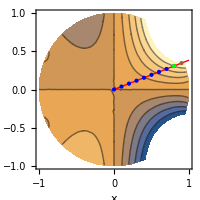

```mathematica
ContourPlot[ prob13,{r,θ}∈Disk[{0,0},1],ImageSize->200,Contours->9,Axes->True,AxesLabel->{x,y},Epilog->{{Red,Line[{{0,0},{1,Sin[π/8]}}]},{Blue,Point[{0.0,0.0 0.38262}]},{Blue,Point[{0.1,0.1 0.38262}]},{Blue,Point[{0.2,0.2 0.38262}]},{Blue,Point[{0.3,0.3 0.38262}]},{Blue,Point[{0.4,0.4 0.38262}]},{Blue,Point[{0.5,0.5 0.38262}]},{Blue,Point[{0.6,0.6 0.38262}]},{Blue,Point[{0.7,0.7 0.38262}]},{Blue,Point[{0.8,0.8 0.38262}]},{Green,Point[{0.8,0.8 0.38262}]},{Brown,Point[{0.9,0.9 0.38262}]}}]
```

This plot did not come out too bad. The function values are semi-believable. If I had chosen θ=π/4 instead of π/8, I might have needed a special test plot section to display the table points.

15.  Φ[1,θ]=1  if -1/2 π<θ<1/2 π and 0 otherwise

```mathematica
Clear["Global`*"]
```

```mathematica
Φ[1,θ_]=Piecewise[{{1, -1/2 π<θ<1/2 π}, {0, θ<-1/2 π∨1/2 π<θ}}]
```

Piecewise[{{1, -π/2<θ<π/2}, {0, True}}]

With my function duly described I need to request a Fourier series

```mathematica
FourierSeries[Φ[1,θ],θ,12];
```

and convert it to trigga franca

```mathematica
ExpToTrig[%]
```

1/2+(2 Cos[θ])/π-(2 Cos[3 θ])/(3 π)+(2 Cos[5 θ])/(5 π)-(2 Cos[7 θ])/(7 π)+(2 Cos[9 θ])/(9 π)-(2 Cos[11 θ])/(11 π)

Again the series comes out well, within an ace of the answer. I need to observe that the angle development is in terms of 2 n-1, affecting both cosine factor and r factor.

```mathematica
Simplify[FindSequenceFunction[{1,-1/3,1/5,-1/7,1/9,-1/11},n]]
```

(-1)^(1+n)/(-1+2 n)

```mathematica
prob15=1/2+2/π Sum[(-1)^(1+n)/(-1+2 n)r^(2n-1)Cos[(2 n-1) θ],{n,1,6}]
```

1/2+(2 (r Cos[θ]-1/3 r^3 Cos[3 θ]+1/5 r^5 Cos[5 θ]-1/7 r^7 Cos[7 θ]+1/9 r^9 Cos[9 θ]-1/11 r^11 Cos[11 θ]))/π

The above answer matches that of the text. This time I anticipated the text’s extraction of 2/πand modified the construction of the sum. The unadorned initial constant has to stand on its own.

Now for the usual table.

```mathematica
Table[{r,r Sin[θ],N[Evaluate[prob15]]},{r,0,0.9,0.1}]/.θ->π/8
```

{{0.,0.,0.5},{0.1,0.0382683,0.558734},{0.2,0.0765367,0.616968},{0.3,0.114805,0.674154},{0.4,0.153073,0.729689},{0.5,0.191342,0.782946},{0.6,0.22961,0.83334},{0.7,0.267878,0.880389},{0.8,0.306147,0.923735},{0.9,0.344415,0.963192}}

And the test plot.

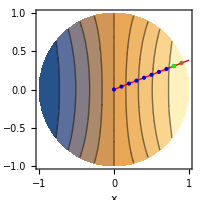

```mathematica
ContourPlot[ prob15,{r,θ}∈Disk[{0,0},1],ImageSize->200,Contours->9,Axes->True,AxesLabel->{x,y},Epilog->{{Red,Line[{{0,0},{1,Sin[π/8]}}]},{Blue,Point[{0.0,0.0 0.38262}]},{Blue,Point[{0.1,0.1 0.38262}]},{Blue,Point[{0.2,0.2 0.38262}]},{Blue,Point[{0.3,0.3 0.38262}]},{Blue,Point[{0.4,0.4 0.38262}]},{Blue,Point[{0.5,0.5 0.38262}]},{Blue,Point[{0.6,0.6 0.38262}]},{Blue,Point[{0.7,0.7 0.38262}]},{Blue,Point[{0.8,0.8 0.38262}]},{Green,Point[{0.8,0.8 0.38262}]},{Brown,Point[{0.9,0.9 0.38262}]}}]
```

Another plot that has at least some credibility.

17.  Φ[1,θ]=θ^2/π^2  if -π<θ<π

```mathematica
Clear["Global`*"]
```

```mathematica
Φ[1,θ_]=Piecewise[{{θ^2/π^2, -π<θ<π}, {0, θ<-π∨π<θ}}]
```

Piecewise[{{θ^2/π^2, -π<θ<π}, {0, True}}]

With my function appropriately described I need to request a Fourier series

```mathematica
FourierSeries[Φ[1,θ],θ,12];
```

and get it into trig form

```mathematica
ExpToTrig[%]
```

1/3-(4 Cos[θ])/π^2+Cos[2 θ]/π^2-(4 Cos[3 θ])/(9 π^2)+Cos[4 θ]/(4 π^2)-(4 Cos[5 θ])/(25 π^2)+Cos[6 θ]/(9 π^2)-(4 Cos[7 θ])/(49 π^2)+Cos[8 θ]/(16 π^2)-(4 Cos[9 θ])/(81 π^2)+Cos[10 θ]/(25 π^2)-(4 Cos[11 θ])/(121 π^2)+Cos[12 θ]/(36 π^2)

The series looks good, and the cosine coefficient development is on a simple ladder. It is a little surprising that the FindSequenceFunction needs eight samples to deduce the coefficient pattern.

```mathematica
Simplify[FindSequenceFunction[{1,-1/4,1/9,-1/16,1/25,-1/36,1/49,-1/64},n]]
```

(-1)^(1+n)/n^2

This time, to coordinate with the text answer, I pull out -4/π^2.

```mathematica
prob17=1/3-4/π^2 Sum[(-1)^(1+n)/n^2 r^n Cos[n θ],{n,1,6}]
```

1/3-(4 (r Cos[θ]-1/4 r^2 Cos[2 θ]+1/9 r^3 Cos[3 θ]-1/16 r^4 Cos[4 θ]+1/25 r^5 Cos[5 θ]-1/36 r^6 Cos[6 θ]))/π^2

The above cell matches the answer in the text. As for the plot, I think the 5th contour is too far left to get centered with additional terms, and I have to attribute its position to the equation itself.

Making up a test table.

```mathematica
Table[{r,r Sin[θ],N[Evaluate[prob17]]},{r,0,0.9,0.1}]/.θ->π/8
```

{{0.,0.,0.333333},{0.1,0.0382683,0.296589},{0.2,0.0765367,0.261176},{0.3,0.114805,0.226995},{0.4,0.153073,0.193951},{0.5,0.191342,0.161943},{0.6,0.22961,0.130854},{0.7,0.267878,0.100531},{0.8,0.306147,0.0707615},{0.9,0.344415,0.0412448}}

Executing a test plot.

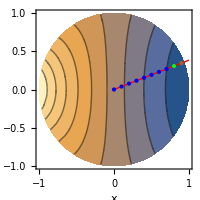

```mathematica
ContourPlot[ prob17,{r,θ}∈Disk[{0,0},1],ImageSize->200,Contours->9,Axes->True,AxesLabel->{x,y},Epilog->{{Red,Line[{{0,0},{1,Sin[π/8]}}]},{Blue,Point[{0.0,0.0 0.38262}]},{Blue,Point[{0.1,0.1 0.38262}]},{Blue,Point[{0.2,0.2 0.38262}]},{Blue,Point[{0.3,0.3 0.38262}]},{Blue,Point[{0.4,0.4 0.38262}]},{Blue,Point[{0.5,0.5 0.38262}]},{Blue,Point[{0.6,0.6 0.38262}]},{Blue,Point[{0.7,0.7 0.38262}]},{Blue,Point[{0.8,0.8 0.38262}]},{Green,Point[{0.8,0.8 0.38262}]},{Brown,Point[{0.9,0.9 0.38262}]}}]
```

The plot looks pretty good, and points meet their swath brackets, but the last two points encounter a very steep plunge.